## Cosmology — Assignment 6 — Finishing the Initial Exploration in Chapter 3

### Problem 1 — Whacky Units

(a) What is the length in the nice, normal units of meters that corresponds to a mass of 1kg in cosmologists’ whacky units?

(b) What is the acceleration in the nice, normal units of m/s^2 that corresponds to 1/second in cosmologists’ whacky units?

(c) What is the diameter of the Earth in seconds?

(d) What is the diameter of the Sun in seconds?

(e) What is the mass of the Sun in seconds?

### Problem 2 — Astronaut Stretching

On the last assignment, we did parts A, B, and C of TWB Chapter 3, Problem 5. Now we’re doing the rest.

In Newtonian mechanics, energy conservation often allows you to solve problems quickly. The formula for the total energy (which is kinetic energy plus potential energy) of a falling astronaut in Newtonian mechanics is:

E=K+U

where the kinetic energy of the astronaut is

K=1/2 m_astronaut v^2

and the potential energy of the astronaut is

U=-(G m_astronaut M)/r

(a) Put in r=∞ and v=0 into the these formula.

(b) With those values, what is E? This is the total energy of an astronaut falling from ∞, starting from rest.

(c) Since the total energy does not change, 0=K+U must be satisfied for all r and v. Solve this equation for v to find v at r=r_ouch.

(d) TWB Chapter 3, Problem 5, p. 3-38, Part D.

(e) TWB Chapter 3, Problem 5, p. 3-38, Part E.

(f) TWB Chapter 3, Problem 5, p. 3-38, Part F.

### Problem 3 — Embedding the [r, ϕ]-Slice Outside the Event Horizon

For this problem we start with the metric in Eq. (6): (Δσ)^2=-(1-2M/r)(Δt)^2+(Δr)^2/(1-2M/r)+(r^2(Δϕ))^2.

(a) Rewrite the metric with the simplification Δt=0. That is the simplification that puts us on an [r, ϕ] slice.

(b) The whole situation is rotationally symmetric. What I mean by that is that nothing depends on ϕ. Let’s analyze the situation with Δϕ=0 too. Later we can imagine bringing back ϕ. Make the further simplification of the metric Δϕ=0.

(c) Take the square root of both sides. Three points to remember:

(i) This problem is specifically exploring the metric outside the event horizon. So r>2M, and therefore 1-2M/r is a positive number,
(ii)  Δσ is a distance, and distances are always positive, so you can use √((Δσ)^2)=Δσ, but 
(iii) Δr is a coordinate difference, and coordinate differences can be positive or negative, so be careful when simplifying √((Δr)^2).

(d) We are going to be marching inward in the r coordinate. Take the correct sign in Part (c) so that negative Δr results in positive Δσ.

DISCUSSION: Remember in class how I was having trouble keeping the minus signs straight when marching inwards? Too many minus signs! Well, here, together, we are going to take the time to do it carefully and get all the signs right.

(e) One last simplification. Let’s measure everything in terms of M. So make a new distance measurement Δs=Δσ/M, and a new radial coordinate x=r/M. Of course x=r/M implies that Δx=Δr/M. Show that

Δs=-Δx/(√(1-2/x))

DISCUSSION: To calculate a total distance, we need to do this on a lot of small local patches, each with a small Δx, and then sum up the corresponding little Δ s_i to get a total distance. In equations:

total distance=∑_(i=o)^(n-1) Δ s_i=∑_(i=0)^(n-1) -Δx/(√(1-2/x)).

(f) We will start at x=7.0 and finish at x=2.2. We will do that in 12 steps of Δx=-0.4 each. Fill in the rightmost two columns of the table table below using:

Δ s_i=-Δx/(√(1-2/x_i))

Two-decimal-place accuracy is fine for the Δ s_i. Round to nearest mm when computing 25 Δ s_i. The conversion to mm is for the plot on the following page. Start your gravity well in the far upper-right of the graph and work your way inwards.

```mathematica
table = Table[{i, 7.0 - 0.4i,-0.4,"    -10", If[True,"",Round[0.4/Sqrt[1-2/(7-0.4i)],0.01]], If[True,"",Round[25 0.4/Sqrt[1-2/(7-0.4i)]]]},{i, 0,11, 1}];
tableWithHeader = PrependTo[table,{"i","x_i"," Δx_","25*Δx_ (for mm)" ,"     Δs_i     ", "25*Δs_i (for mm)"}];
TableForm[tableWithHeader]
```

i | x_i |  Δx_ | 25*Δx_ (for mm) |      Δs_i      | 25*Δs_i (for mm)
0 | 7. | -0.4 |     -10 |  | 
1 | 6.6 | -0.4 |     -10 |  | 
2 | 6.2 | -0.4 |     -10 |  | 
3 | 5.8 | -0.4 |     -10 |  | 
4 | 5.4 | -0.4 |     -10 |  | 
5 | 5. | -0.4 |     -10 |  | 
6 | 4.6 | -0.4 |     -10 |  | 
7 | 4.2 | -0.4 |     -10 |  | 
8 | 3.8 | -0.4 |     -10 |  | 
9 | 3.4 | -0.4 |     -10 |  | 
10 | 3. | -0.4 |     -10 |  | 
11 | 2.6 | -0.4 |     -10 |  |

CROSS-CHECK AND DISCUSSION: You can check your work against mine by summing all the little distances Δ s_i and checking that the total distance is about 6.75. To summarize, we marched inwards a total r-coordinate change of 12*(-0.4M)=-4.8M, but the physical distance corresponding to that coordinate change was 6.75M.

UNITS: These statements and what follows are understood to be in units of M, the black hole’s mass.

(g) Now it is time to make a beautiful embedding diagram. You will need a ruler with a millimeter scale. For an embedding, we imagine an additional coordinate that is entirely fictional. It is just to help us visualize curved spacetime. We’ll will call this entirely fictional coordinate z. On the horizontal axis we plot x. A step of Δ x_i=-0.4 in Δx is just a step to the left. But we need to make that step have a physical distance of Δ s_i. So we go down along the fictional z-direction however much it takes to make Δ s_i the right amount. That is what TWB are showing in Fig. 11 on p. 3-30. Below is a graph for you to make a beautiful radial profile with the 12 steps you calculated above. You have to multiply all the distances by 25mm to put on the plot below. That is why you did the final column in the table.

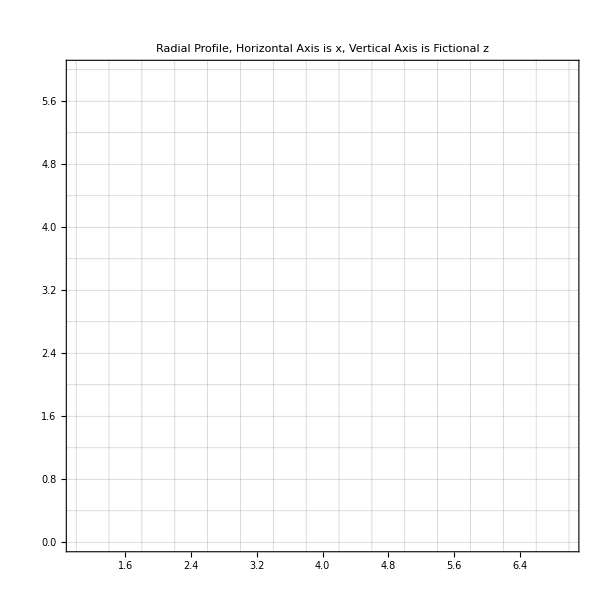

```mathematica
Plot[{},{x, 0, 8}, PlotRange->{{1, 7},{0,6}}, AspectRatio->1, GridLines->{Range[1,7,0.4],Range[0,6,0.4]}, Frame->True, PlotLabel->"Radial Profile, Horizontal Axis is x, Vertical Axis is Fictional z"]
```

### Problem 4 — Exploring Light-Like Worldlines of the [r, ϕ]-Slice Inside the Event Horizon

We start with the metric in Eq. (5): (Δτ)^2=(1-2M/r)(Δt)^2-(Δr)^2/(1-2M/r)-(r^2(Δϕ))^2.

(a) Inside the event horizon, 1-2M/r is negative. Rewrite the metric to make it clearer that the coefficient of (Δt)^2 is negative and the coefficient of (Δr)^2 is positive. (Don’t overthink this. It is just re-distributing some minus signs.)

(b) So moving around in the global-r coordinate now adds to wristwatch time, whereas moving around in the global-t coordinate subtracts from wristwatch time. That means that the r coordinate behaves like a time coordinate in this region! We are going to restrict ourselves to the [r, ϕ]-slice as we did in Problem 4. So set Δt=0 and simplify, but conceptually, keep in mind that in this region, what you have done is get rid of a spatial coordinate!

(c) We want to study the behavior of light-like world-lines. For light, Δτ=0. Make that simplification. Also, rearrange and then do a careful taking of square roots.

(d) We are going to focus on black holes, not white holes, and we are going to simplify to light spiraling inward in the increasing ϕ direction. That is the only case we are interested in present. Solve what you got in (c) for Δϕ, and also choose the signs so that increasing Δϕ results in decreasing Δr.

(e) As in Problem 3, we are going to introduce a new dimensionless global coordinate x=r/M, and of course it follows that Δx=Δr/M. Rewrite your equation with this new coordinate. Show that:

Δϕ=-Δx/(x √(2/x-1))

(f) We will start at x=1.5 and finish at x=0.0. We will do that in 15 steps of Δx=-0.1 each. Fill in the final three columns of the table table below using:

Δ ϕ_i=-Δx/(x_i √(2/x_i-1))

Three-decimal-place accuracy is good for the Δ ϕ_i. Round to nearest tenth of a degree when computing 360/(2π) Δ ϕ_i. Start your world-line at x=1.5, ϕ=0 and work your way inward. In the final column, put the running cumulative change in ϕ (in degrees).

```mathematica
table2 = Table[{i, 1.5 - 0.1i,-0.1, If[True,"",Round[0.1/(1.5-0.1i)/Sqrt[2/(1.5-0.1i)-1],0.001]], If[True,"",Round[360 / 2 / π *0.1/ (1.5-0.1i)/Sqrt[2/(1.5-0.1i)-1],0.1]]},{i, 0,14, 1}];
table2WithHeader = PrependTo[table2,{"i","x_i"," Δx_" ,"        Δϕ_i   ", "360/(2  π)*Δϕ_i (degrees)", "Cumulative change in ϕ"}];
TableForm[table2WithHeader]
```

i | x_i |  Δx_ |         Δϕ_i    | 360/(2  π)*Δϕ_i (degrees) | Cumulative change in ϕ
0 | 1.5 | -0.1 |  |  | 
1 | 1.4 | -0.1 |  |  | 
2 | 1.3 | -0.1 |  |  | 
3 | 1.2 | -0.1 |  |  | 
4 | 1.1 | -0.1 |  |  | 
5 | 1. | -0.1 |  |  | 
6 | 0.9 | -0.1 |  |  | 
7 | 0.8 | -0.1 |  |  | 
8 | 0.7 | -0.1 |  |  | 
9 | 0.6 | -0.1 |  |  | 
10 | 0.5 | -0.1 |  |  | 
11 | 0.4 | -0.1 |  |  | 
12 | 0.3 | -0.1 |  |  | 
13 | 0.2 | -0.1 |  |  | 
14 | 0.1 | -0.1 |  |  |

(g) Finally, it is time to make a beautiful world line. Start at x=1.5 (the 15th concentric circle) and ϕ=0° and work your way inwards 0.1 at a time.

```mathematica
PolarPlot[{2},{x, 0, 2π}, PolarGridLines->{Automatic,Range[0,2, 0.1]}, PlotLabel->"Worldline for a Light-Like Particle on an [Cell["r",ExpressionUUID->"ac715546-214c-48e0-a8d1-a7a78be34778"],ϕ]-Slice Inside the Event Horizon", PolarAxes->Automatic, PolarTicks->{"Degrees", Automatic}, PlotRange->2,PlotRangePadding->1.25]
```

-Graphics-